```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_moments_deal/Mathematica_files

```mathematica
<<NDSolve`FEM`
```

## Importing data

```mathematica
(*numerical solution, flag == 0, exact solution, flag == 1 and error flag == 2*)
importdata[dof_,p_,refinetype_,flag_,outputdir_]:=Module[{result,filename},
Which[flag == 0,
filename=StringJoin["../",outputdir,"/solution/numerical_solution",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],

flag == 1,
filename=StringJoin["../",outputdir,"/solution/exact_solution",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],

flag == 2,
filename=StringJoin["../",outputdir,"/solution/error",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]]
];

result = Import[filename,"Table"][[2;;-1,All]]
]
```

## Solution

### G26 A

```mathematica
solution = importdata[4800,1,"_global_",0,"output_trial"];
ListPlot3D[solution⟦All,{1,2,3}⟧,PlotRange->All,ClippingStyle->True,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],Mesh->True,InterpolationOrder->3,ImageSize->400,PlotLabel->"deviation of temperature",PlotLegends->Automatic,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

### G26

#### exact solution

```mathematica
(*theta,delta,q,sigma,R,m*)
U26θW1[x_] :={-1.3193576588506577-0.548685702383432 x^2+0.13608276348795437 x^4+0.09005797246678635 Cosh[2.191140660407265 x]-6.938893903907228*^-18 Sinh[2.191140660407265 x],-0.21908902300206642 x^2,-1/3 √(2/5) x^3,-0.07331283107342124-0.1131370849898476 x^2+0.06499374330796374 Cosh[2.191140660407265 x],0.03918735656159667+0.21166010488516723 x^2-0.03474061710604745 Cosh[2.191140660407265 x],0.+0.14109060918431104 x-0.05708465895189606 Sinh[2.191140660407265 x]};

U26θW0[x_]:={-0.09461278745906829-0.548685702383432 x^2+0.13608276348795437 x^4+0.09005797246678635 Cosh[2.191140660407265 x],-0.21908902300206642 x^2,-1/3 √(2/5) x^3,-0.07331283107342124-0.1131370849898476 x^2+0.06499374330796374 Cosh[2.191140660407265 x],0.03918735656159667+0.21166010488516723 x^2-0.03474061710604745 Cosh[2.191140660407265 x],0.14109060918431104 x-0.05708465895189606 Sinh[2.191140660407265 x]};
```

#### Numerical solution

```mathematica
solution = importdata[61200,1,"_global_",0,"output_trial_G26"];
(*rho,vx,vy,θ,σxx,σxy,σyy,qx,qy,mxxx,mxxy,mxyy,myyy,Δ,Rxx,Rxy,Ryy*)

ListPlot3D[-√(2/3)solution⟦All,{1,2,6}⟧,PlotRange->{All,{-0.5,0.5}},ClippingStyle->True,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],Mesh->True,InterpolationOrder->3,ImageSize->400,PlotLabel->"deviation of temperature",PlotLegends->Automatic,AxesLabel->{"x","y","z"}]

ListPlot3D[solution⟦All,{1,2,11}⟧,PlotRange->All,ClippingStyle->True,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],Mesh->True,InterpolationOrder->3,ImageSize->400,PlotLabel->"heat flux",PlotLegends->Automatic,AxesLabel->{"x","y","z"}]


ListPlot3D[solution⟦All,{1,2,5}⟧,PlotRange->All,ClippingStyle->True,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],Mesh->True,InterpolationOrder->3,ImageSize->400,PlotLabel->"vy",PlotLegends->Automatic,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
N[Sqrt[2/3],15]
```

0.816496580927726

```mathematica
-2/1.3+3
```

1.46154

```mathematica
solution
```

{{-1.,-1.,-1.92612,0.,0.002518,0.222377,-0.743835,0.,1.48767,0.,0.206851,0.,-0.645376,0.,1.29075,-0.218214,0.322306,0.,-0.644611},{-0.333333,-1.,-1.92612,0.,0.002518,0.222377,-0.743835,0.,1.48767,0.,0.206851,0.,-0.645376,0.,1.29075,-0.218214,0.322306,0.,-0.644611},5996,{0.333333,1.,-1.92612,0.,-0.002518,0.222377,-0.743835,0.,1.48767,0.,-0.206851,0.,0.645376,0.,-1.29075,-0.218214,0.322306,0.,-0.644611},{1.,1.,-1.92612,0.,-0.002518,0.222377,-0.743835,0.,1.48767,0.,-0.206851,0.,0.645376,0.,-1.29075,-0.218214,0.322306,0.,-0.644611}}
 |  |  |  |

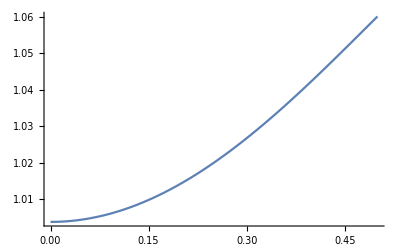

```mathematica
Plot[-√(2/3)U26θW1[x]⟦1⟧,{x,0,0.5}]
```

## Solution New Code

#### G26 A

```mathematica
result = importdata[15360,1,"_global_",0,"Tests/build/output_systemA_Kn10p0"]

exactsolution =  importdata[15360,1,"_global_",1,"Tests/build/output_systemA_Kn10p0"];

error =  importdata[15360,1,"_global_",2,"Tests/build/output_systemA_Kn10p0"]

ListPlot3D[result⟦All,{1,2,3}⟧,RegionFunction->Function[{x,y},0.5^2<x^2+y^2<4]]
ListPlot3D[exactsolution⟦All,{1,2,3}⟧,RegionFunction->Function[{x,y},0.5^2<x^2+y^2<4]]
```

{{2.,0.,1.34706,0.303656,0.003336,-0.024361,-0.001719,0.004391},{1.99384,0.156918,1.34713,0.302246,0.020866,-0.024361,0.000189,0.004412},2557,{0.5,0.,2.21242,-0.159874,-0.000383,-0.032558,-0.000284,0.025075}}
 |  |  |  |

{{2.,0.,1.3364,0.312307,0.,0.,0.,0.},{1.99384,0.156918,1.33601,0.310946,0.02494,0.,0.,0.},{1.8125,0.,1.8428,0.23453,0.,0.,0.,0.},2555,{0.498459,-0.03923,2.20014,-0.167818,0.006804,0.,0.,0.},{0.5,0.,2.20068,-0.168293,0.,0.,0.,0.}}
 |  |  |  |

-Graphics3D-

-Graphics3D-

```mathematica
?RegionFunction
```

RegionFunction is an option for plotting functions that specifies the region to include in the plot drawn.

#### G26 Heat Conduction

```mathematica
dof = 6800;
foldername = "Tests/build/output_G26_trial";
result = importdata[dof,1,"_global_",0,foldername];

exactsolution =  importdata[dof,1,"_global_",1,foldername];
```

```mathematica
ListPlot3D[result⟦All,{1,2,6}⟧]
ListPlot3D[exactsolution⟦All,{1,2,6}⟧]
```

-Graphics3D-

-Graphics3D-

## IDs for different variables

```mathematica
(*we declare the IDs for different variables, this will help us with plotting*)
IDRho = 1+2;
IDvx = 2+2;
IDvy = 3+2;
IDtheta = 4+2;
IDsigmaxx = 5+2;
IDsigmaxy = 6+2;
IDsigmayy = 7+2;
IDqx = 8+2;
IDqy = 9+2;
```

## Mapping to Primitive variables

```mathematica
(*we change the numerical solution obtained to the primitive variables.*)
ConvToPrim[sol_]:=Module[{factorθ,factorσ,factorq,trialsol},
trialsol = sol;
factorθ = -√(2/3);
factorσ = √2;
factorq = -√(5/2);
trialsol⟦All,IDtheta⟧ =factorθ * sol⟦All,IDtheta⟧;
trialsol⟦All,{IDqx,IDqy}⟧ =factorq*sol⟦All,{IDqx,IDqy}⟧;
trialsol⟦All,{IDsigmaxx,IDsigmaxy,IDsigmayy}⟧=factorσ*sol⟦All,{IDsigmaxx,IDsigmaxy,IDsigmayy}⟧;

trialsol
]
```

## Solution Poisson Heat

### G56

```mathematica
ndof=13600;
foldername = "Tests/build/output_G56_odd_Kn0p1";
numsol56=importdata[ndof,1,"_global_",0,foldername];
error56=importdata[ndof,1,"_global_",2,foldername];
exactsol56=importdata[ndof,1,"_global_",1,foldername];
```

```mathematica
ListPlot3D[numsol56⟦All,{1,2,6}⟧,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[exactsol56⟦All,{1,2,6}⟧,PlotRange->All]
```

-Graphics3D-

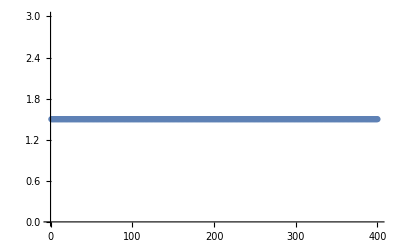

```mathematica
ListPlot[-√(3/2)numsol56⟦All,6⟧]
```

### G45

```mathematica
ndof=11200;
foldername = "Tests/build/output_G45_odd_Kn0p1";
numsol45=importdata[ndof,1,"_global_",0,foldername];
error45=importdata[ndof,1,"_global_",2,foldername];
(*exactsol45=importdata[ndof,1,"_global_",1,foldername];*)
```

```mathematica
ListPlot[-√(3/2)numsol45⟦All,6⟧]
```

-Graphics-

## Solution Heated Cavity

### G20

```mathematica
ndof=32500;
foldername = "Tests/build/output_G20_char_Kn0p1";
numsol20=importdata[ndof,1,"_global_",0,foldername];
```

```mathematica
ListPlot3D[numsol20⟦All,{1,2,4}⟧,ColorFunction->Hue,PlotRange->Full]
```

-Graphics3D-

## Solution Lid Driven

### G20

```mathematica
ndof=130000;
foldername = "Tests/build/output_G20_odd_Kn0p1";
numsol20=importdata[ndof,1,"_global_",0,foldername];
numsol20 = ConvToPrim[numsol20];
```

#### vx

```mathematica
ListPlot3D[numsol20⟦All,{1,2,IDvx}⟧,ColorFunction->Hue,PlotRange->Full]
```

-Graphics3D-

#### vy

```mathematica
ListPlot3D[numsol20⟦All,{1,2,IDvy}⟧,ColorFunction->Hue,PlotRange->Full]
```

-Graphics3D-

#### θ

```mathematica
ListPlot3D[numsol20⟦All,{1,2,IDtheta}⟧,ColorFunction->Hue,PlotRange->Full,ViewPoint->Above]
```

-Graphics3D-

#### qx

```mathematica
ListPlot3D[numsol20⟦All,{1,2,IDqx}⟧,ColorFunction->Hue,PlotRange->Full]
```

-Graphics3D-

#### qy

```mathematica
ListPlot3D[numsol20⟦All,{1,2,IDqy}⟧,ColorFunction->Hue,PlotRange->Full]
```

-Graphics3D-

#### sigmaxx

```mathematica
ListPlot3D[numsol20⟦All,{1,2,IDsigmaxx}⟧,ColorFunction->Hue,PlotRange->Full]
```

-Graphics3D-

#### sigmaxy

```mathematica
ListPlot3D[numsol20⟦All,{1,2,IDsigmaxy}⟧,ColorFunction->Hue,PlotRange->Full,PlotLegends->Automatic]
```

-Graphics3D-

#### sigmayy

```mathematica
ListPlot3D[numsol20⟦All,{1,2,IDsigmayy}⟧,ColorFunction->Hue,PlotRange->Full]
```

-Graphics3D-

#### Velocity field

```mathematica
(*in the velocity field we store the velocity vector at the particular point x and y*)
velocityfield = Table[{{numsol20⟦ii,1⟧,numsol20⟦ii,2⟧},{numsol20⟦ii,IDvx⟧,numsol20⟦ii,IDvy⟧}},{ii,1,Length[numsol20]}];
```

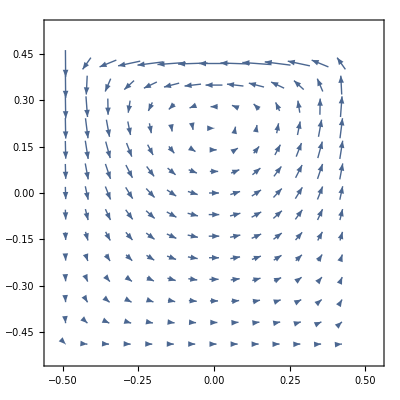

```mathematica
ListVectorPlot[velocityfield]
```

#### Heat flow filed

```mathematica
(*in the velocity field we store the velocity vector at the particular point x and y*)
heatfluxfield = Table[{{numsol20⟦ii,1⟧,numsol20⟦ii,2⟧},{numsol20⟦ii,IDqx⟧,numsol20⟦ii,IDqy⟧}},{ii,1,Length[numsol20]}];
```

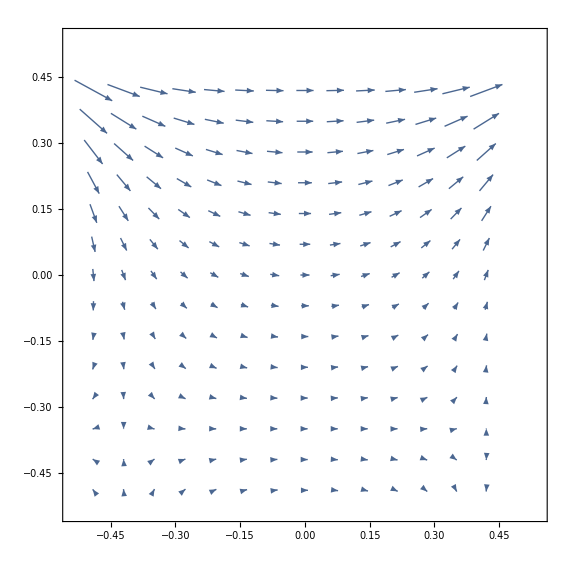

```mathematica
ListVectorPlot[heatfluxfield]
```

## Solution Square Circular Cavity

### G20

```mathematica
ndof=26624;
foldername = "Tests/build/output_G20_odd_Kn1p0";
numsol20=importdata[ndof,1,"_global_",0,foldername];
numsol20 = ConvToPrim[numsol20];
```

#### vx

```mathematica
ListPlot3D[numsol20⟦All,{1,2,IDvx}⟧,ColorFunction->Hue,PlotRange->Full,RegionFunction->Function[{x,y,z},0.266<√(x^2+y^2)],ViewPoint->Top]
```

-Graphics3D-

#### vy

```mathematica
ListPlot3D[numsol20⟦All,{1,2,IDvy}⟧,ColorFunction->Hue,PlotRange->Full,RegionFunction->Function[{x,y,z},0.266<√(x^2+y^2)]]
```

-Graphics3D-

#### θ

```mathematica
ListPlot3D[numsol20⟦All,{1,2,IDtheta}⟧,ColorFunction->Hue,PlotRange->Full,ViewPoint->Above,RegionFunction->Function[{x,y,z},0.266<√(x^2+y^2)]]
```

-Graphics3D-

#### qx

```mathematica
ListPlot3D[numsol20⟦All,{1,2,IDqx}⟧,ColorFunction->Hue,PlotRange->Full,RegionFunction->Function[{x,y,z},0.266<√(x^2+y^2)]]
```

-Graphics3D-

#### qy

```mathematica
ListPlot3D[numsol20⟦All,{1,2,IDqy}⟧,ColorFunction->Hue,PlotRange->Full,RegionFunction->Function[{x,y,z},0.266<√(x^2+y^2)]]
```

-Graphics3D-

#### sigmaxx

```mathematica
ListPlot3D[numsol20⟦All,{1,2,IDsigmaxx}⟧,ColorFunction->Hue,PlotRange->Full,RegionFunction->Function[{x,y,z},0.266<√(x^2+y^2)]]
```

-Graphics3D-

#### sigmaxy

```mathematica
ListPlot3D[numsol20⟦All,{1,2,IDsigmaxy}⟧,ColorFunction->Hue,PlotRange->Full,PlotLegends->Automatic]
```

-Graphics3D-

#### sigmayy

```mathematica
ListPlot3D[numsol20⟦All,{1,2,IDsigmayy}⟧,ColorFunction->Hue,PlotRange->Full]
```

-Graphics3D-

#### Velocity field

```mathematica
(*in the velocity field we store the velocity vector at the particular point x and y*)
velocityfield = Table[{{numsol20⟦ii,1⟧,numsol20⟦ii,2⟧},{numsol20⟦ii,IDvx⟧,numsol20⟦ii,IDvy⟧}},{ii,1,Length[numsol20]}];
```

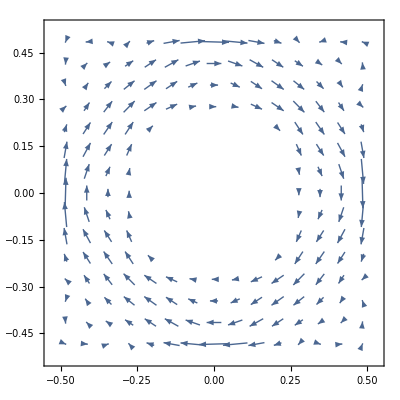

```mathematica
ListVectorPlot[velocityfield,RegionFunction->Function[{x,y,z},0.266<√(x^2+y^2)]]
```

#### Heat flow filed

```mathematica
(*in the velocity field we store the velocity vector at the particular point x and y*)
heatfluxfield = Table[{{numsol20⟦ii,1⟧,numsol20⟦ii,2⟧},{numsol20⟦ii,IDqx⟧,numsol20⟦ii,IDqy⟧}},{ii,1,Length[numsol20]}];
```

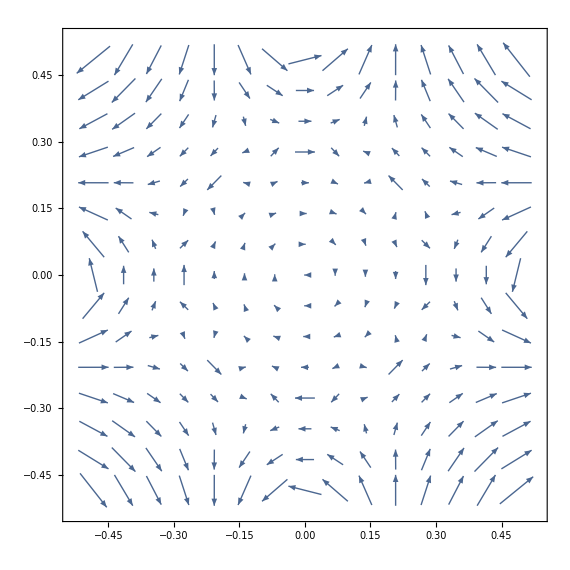

```mathematica
ListVectorPlot[heatfluxfield]
```

## Plotting help

### Reading the mesh

```mathematica
(*In the following function we read the gmsh file*)
ReadMeshFile[filename_]:=Import[filename,"Table"];

(*In the following function we extract the coordinates for the vertices*)
ExtractVertices[mesh_]:=Module[{nVerts,verts,offset},
(*offset from the gmsh *)
offset = 5;

(*total number of vertices in the mesh*)
nVerts = mesh⟦offset⟧⟦1⟧;

(*vertices of the mesh*)
verts = mesh⟦offset+1;;offset+nVerts,All⟧;

(*now we only extract the coordinates*)
verts⟦All,2;;-1⟧
]

(*In the following function we extract the elements*)
ExtractElements[mesh_]:=Module[{nElm,Elm,beginElm,beginQuads,offset},
(*location where the elements begin*)
beginElm = Position[mesh,"$Elements"]⟦1,1⟧;

(*Extract all the elements. This includes the physical groups which were defined during the mesh generation*)
Elm=mesh⟦beginElm;;-1,All⟧;

(*location where the actual quads begin, 3 because of the offset and 4 because that stores the ID of the physical entity.
The value 3 in the checks whether we have a quad or not
*)
offset = 3;
Do[If[Length[Elm⟦ii⟧]≥5,If[Elm⟦ii⟧⟦2⟧==3,beginQuads=ii; Break[];Print["Inside"];]],{ii,1,Length[Elm]}];

(*from begin quads to -2 because the last element in $EndElements*)
Elm = Elm⟦beginQuads;;-2,6;;-1⟧;

Elm
]

(*In the following routine we check the mesh which we have read from the file*)
CheckElms[Elms_,nVerts_]:=Module[{},

(*We check whether all the vertices have been included or not in the connectivity data*)

If[Norm[DeleteDuplicates[Sort[Flatten[Elms]]]-Range[1,nVerts]]==0,Print[Style["Correct Mesh",FontColor->Green]],Print[Style["InCorrect Mesh",FontColor->Red]]]
];


CreateMesh[mesh_,dim_]:=Module[{Verts,Elms,OrderedVerts,nVerts,finalMesh},

Verts = ExtractVertices[mesh]⟦All,1;;dim⟧;
nVerts = Length[Verts];
Elms = ExtractElements[mesh];

CheckElms[Elms,nVerts];
finalMesh = ToElementMesh["Coordinates"->Verts,"MeshElements"->{QuadElement[Elms]}];

finalMesh
]
```

### Interpolation

```mathematica
InterpolateSolution[solution_]:=Module[{densityData,vxData,vyData,thetaData,sigmaxxData,sigmaxyData,sigmayyData,qxData,qyData},

(*convert data into a format which is read by Interpolation*)
densityData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDRho⟧},{ii,1,Length[solution]}];

vxData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDvx⟧},{ii,1,Length[solution]}];

vyData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDvy⟧},{ii,1,Length[solution]}];

thetaData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDtheta⟧},{ii,1,Length[solution]}];

sigmaxxData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDsigmaxx⟧},{ii,1,Length[solution]}];

sigmaxyData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDsigmaxy⟧},{ii,1,Length[solution]}];

sigmayyData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDsigmayy⟧},{ii,1,Length[solution]}];

qxData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDqx⟧},{ii,1,Length[solution]}];

qyData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDqy⟧},{ii,1,Length[solution]}];

(*remove the duplicate entries for Interpolation function*)
densityData = DeleteDuplicatesBy[densityData,First];
vxData = DeleteDuplicatesBy[vxData,First];
vyData = DeleteDuplicatesBy[vyData,First];
thetaData = DeleteDuplicatesBy[thetaData,First];
sigmaxxData = DeleteDuplicatesBy[sigmaxxData,First];
sigmaxyData = DeleteDuplicatesBy[sigmaxyData,First];
sigmayyData = DeleteDuplicatesBy[sigmayyData,First];
qxData = DeleteDuplicatesBy[qxData,First];
qyData = DeleteDuplicatesBy[qyData,First];

densityData=Interpolation[densityData,InterpolationOrder->1];
vxData=Interpolation[vxData,InterpolationOrder->1];
vyData=Interpolation[vyData,InterpolationOrder->1];
thetaData=Interpolation[thetaData,InterpolationOrder->1];
sigmaxxData=Interpolation[sigmaxxData,InterpolationOrder->1];
sigmaxyData=Interpolation[sigmaxyData,InterpolationOrder->1];
sigmayyData=Interpolation[sigmayyData,InterpolationOrder->1];
qxData=Interpolation[qxData,InterpolationOrder->1];
qyData=Interpolation[qyData,InterpolationOrder->1];

{densityData,vxData,vyData,thetaData,sigmaxxData,sigmaxyData,sigmayyData,qxData,qyData}
]
```

### Plot Contour

```mathematica
PlotContour[data_,domain_,ratio_]:=Module[{},

ContourPlot[data[x,y],{x,y}∈domain,ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,AspectRatio->1/ratio,ContourLabels->True]
]
```

### Plot Streamlines

```mathematica
PlotStreamlines[data_,domain_,ratio_]:=Module[{},
StreamPlot[{data⟦1⟧[x,y],data⟦2⟧[x,y]},{x,y}∈domain,PlotRange->Full,ColorFunction->Hue,AspectRatio->1/ratio]]
```

### Plot Vector

```mathematica
PlotVectorlines[data_,domain_,ratio_]:=Module[{},
VectorPlot[{data⟦1⟧[x,y],data⟦2⟧[x,y]},{x,y}∈domain,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,AspectRatio->1/ratio]]
```

## Solution NACA501

### Create mesh

```mathematica
NACA5012Data = ReadMeshFile["../NACA/NACA5012.msh"];
NACA5012Mesh = CreateMesh[NACA5012Data,2];
```

Correct Mesh

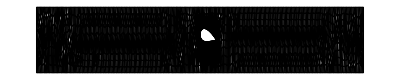

```mathematica
NACA5012Mesh["Wireframe"["MeshElementStyle"->EdgeForm[{Thin,Black}]]]
```

### G20

```mathematica
ndof=91988;
foldername = "Tests/build/output_G20_odd_Kn1p0";
numsol20=importdata[ndof,1,"_global_",0,foldername];
numsol20 = ConvToPrim[numsol20];
```

#### interpolated data

```mathematica
solution20 = InterpolateSolution[numsol20];
```

#### vx

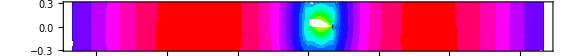

```mathematica
PlotContour[solution20⟦IDvx-2⟧,MeshRegion[NACA5012Mesh],10]
```

#### vy

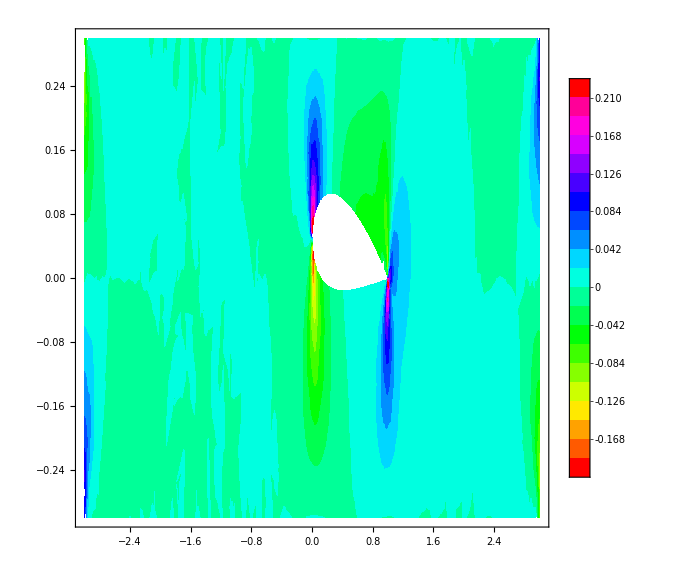

```mathematica
PlotContour[solution20⟦IDvy-2⟧,MeshRegion[NACA5012Mesh]]
```

#### θ

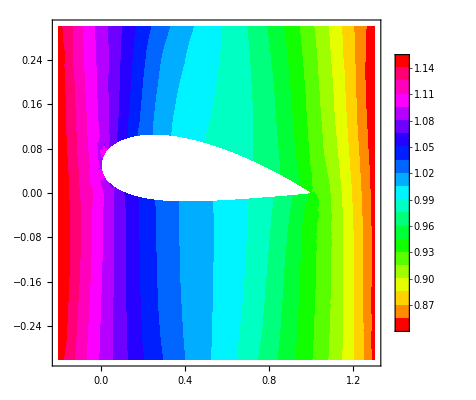

```mathematica
PlotContour[solution20⟦IDtheta-2⟧,MeshRegion[NACA5012Mesh]]
```

#### qx

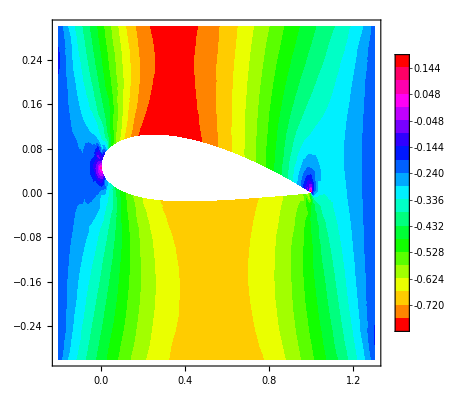

```mathematica
PlotContour[solution20⟦IDqx-2⟧,MeshRegion[NACA5012Mesh]]
```

#### qy

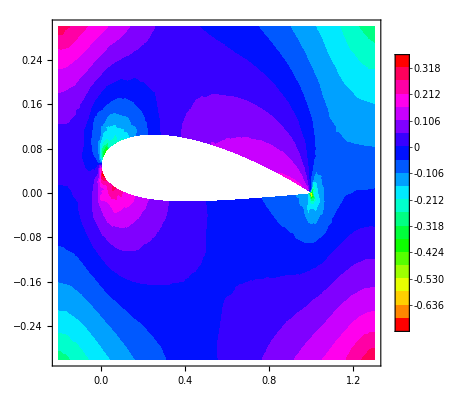

```mathematica
PlotContour[solution20⟦IDqy-2⟧,MeshRegion[NACA5012Mesh]]
```

#### sigmaxx

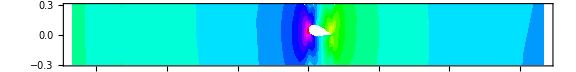

```mathematica
PlotContour[solution20⟦IDsigmaxx-2⟧,MeshRegion[NACA5012Mesh],8]
```

#### sigmaxy

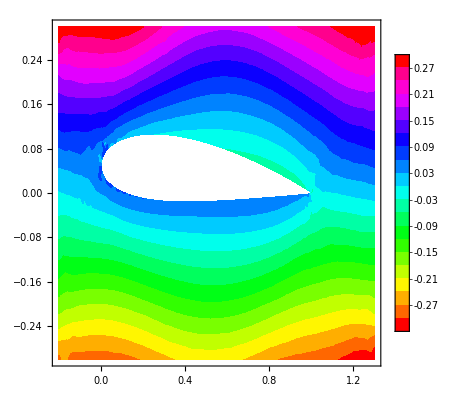

```mathematica
PlotContour[solution20⟦IDsigmaxy-2⟧,MeshRegion[NACA5012Mesh]]
```

#### sigmayy

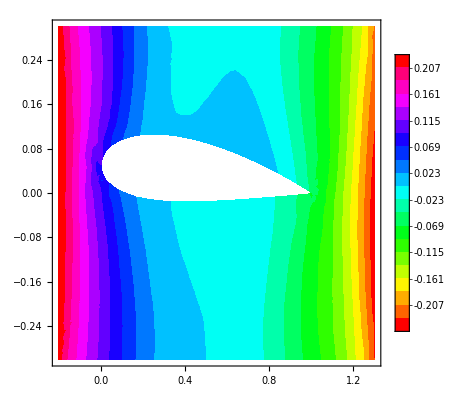

```mathematica
PlotContour[solution20⟦IDsigmayy-2⟧,MeshRegion[NACA5012Mesh]]
```

#### Velocity field

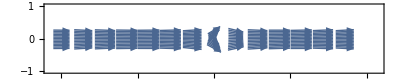

```mathematica
(*in the velocity field we store the velocity vector at the particular point x and y*)
Show[PlotVectorlines[solution20⟦{IDvx-2,IDvy-2}⟧,MeshRegion[NACA5012Mesh],5]]
```

#### Heat flow filed

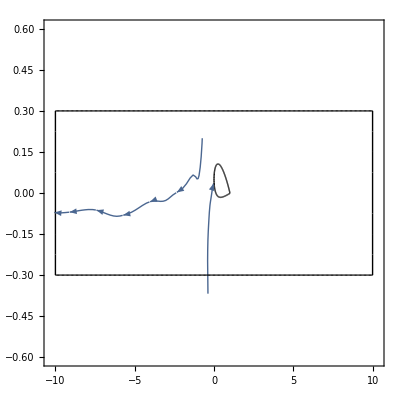

```mathematica
(*in the velocity field we store the velocity vector at the particular point x and y*)
Show[PlotStreamlines[solution20⟦{IDqx-2,IDqy-2}⟧,MeshRegion[NACA5012Mesh]],NACA5012Mesh["Wireframe"["MeshElement"->"BoundaryElements"]]]
```

## Solution Free Flow cylinder

### Create mesh

```mathematica
SquareCylinderData = ReadMeshFile["../square_circular_cavity_channel/square_circular_cavity.msh"];
SquareCylinderMesh = CreateMesh[SquareCylinderData,2];
```

Correct Mesh

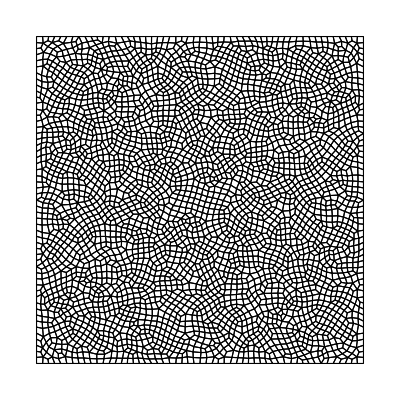

```mathematica
MeshPlot=SquareCylinderMesh["Wireframe"["MeshElementStyle"->EdgeForm[{Thin,Black}]]]
```

### G20

```mathematica
ndof=191568;
foldername = "Tests/build/output_G20_odd_Kn0p1";
numsol20=importdata[ndof,1,"_global_",0,foldername];
numsol20 = ConvToPrim[numsol20];
mesh = SquareCylinderMesh;
```

#### interpolated data

```mathematica
solution20 = InterpolateSolution[numsol20];
```

#### vx

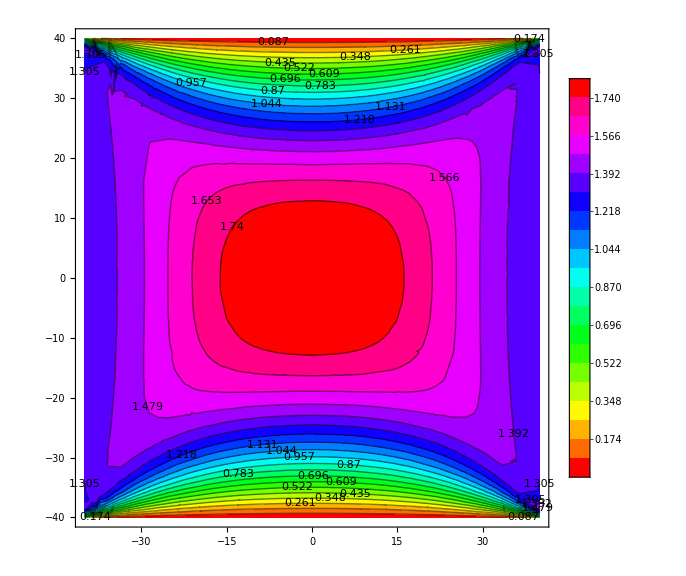

```mathematica
PlotContour[solution20⟦IDvx-2⟧,MeshRegion[mesh],1]
```

#### vy

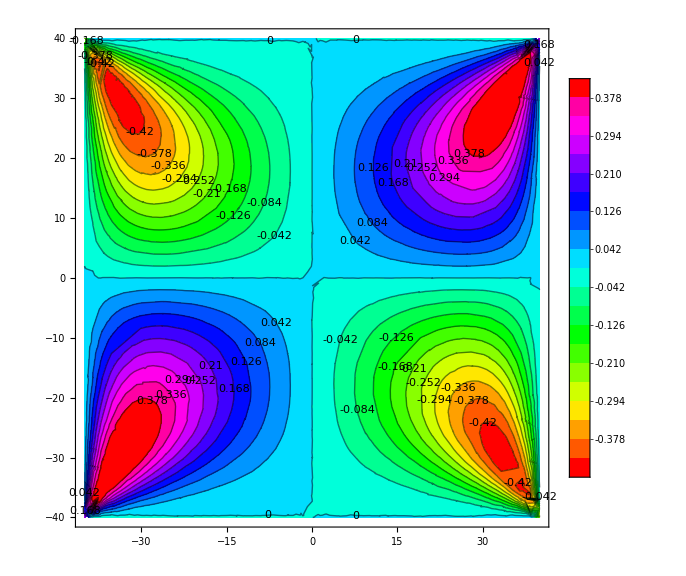

```mathematica
PlotContour[solution20⟦IDvy-2⟧,MeshRegion[mesh],1]
```

#### θ

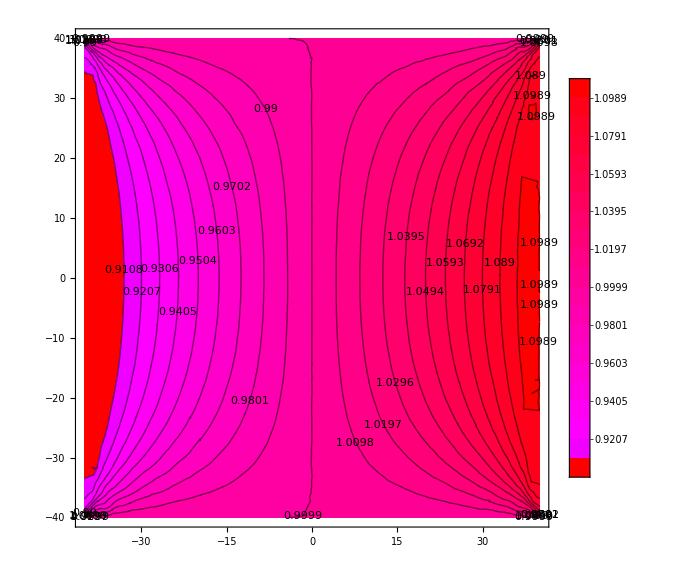

```mathematica
PlotContour[solution20⟦IDtheta-2⟧,MeshRegion[mesh],1]
```

#### qx

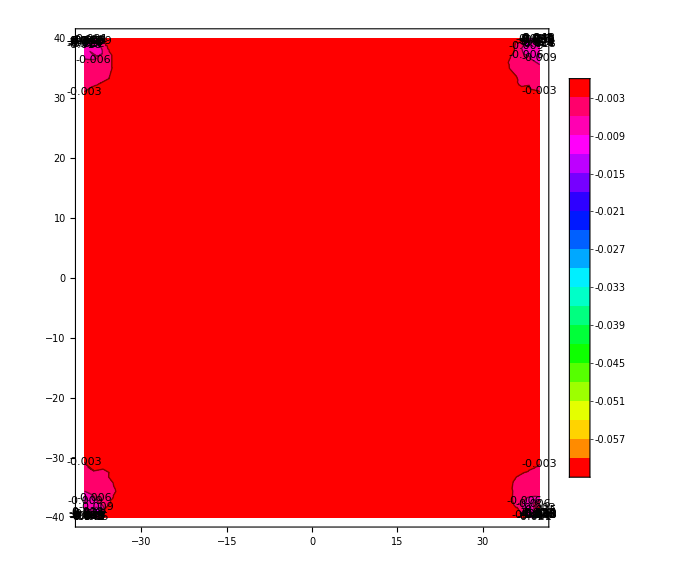

```mathematica
PlotContour[solution20⟦IDqx-2⟧,MeshRegion[mesh],1]
```

#### qy

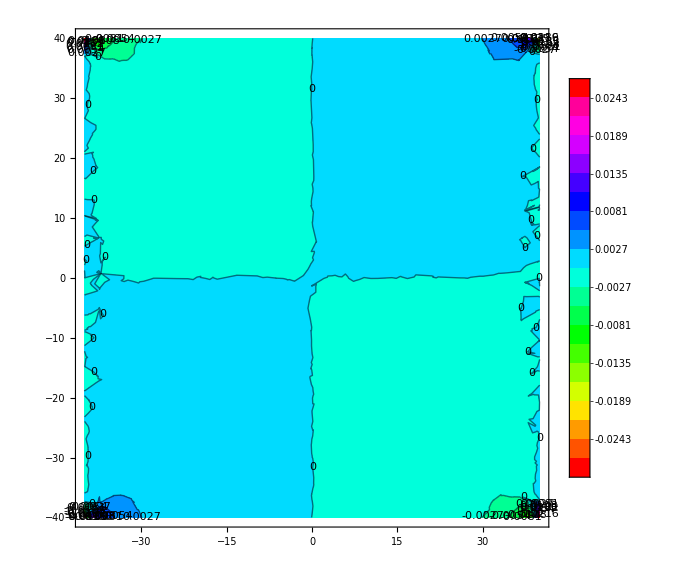

```mathematica
PlotContour[solution20⟦IDqy-2⟧,MeshRegion[mesh],1]
```

#### sigmaxx

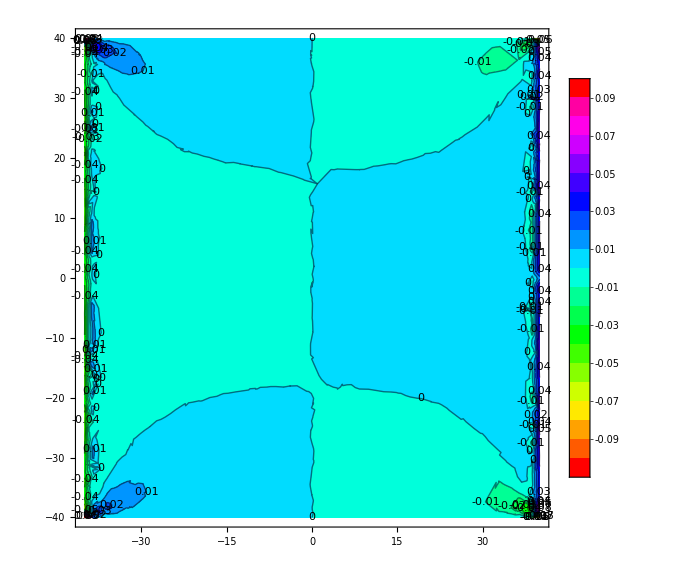

```mathematica
PlotContour[solution20⟦IDsigmaxx-2⟧,MeshRegion[mesh],1]
```

#### sigmaxy

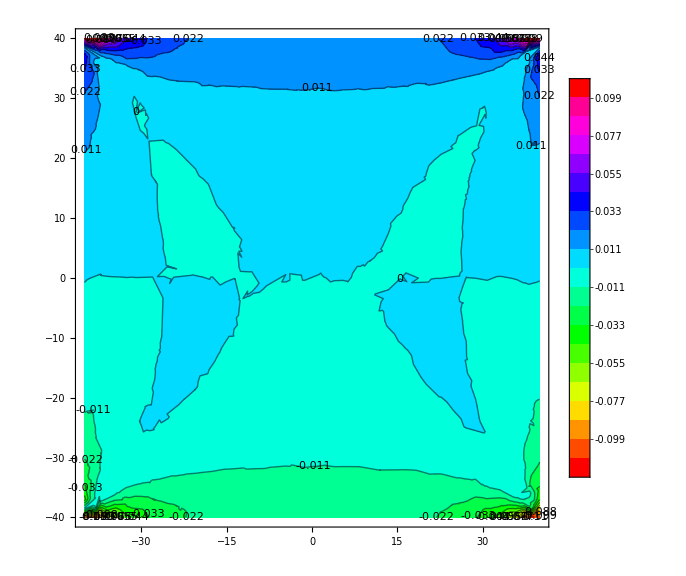

```mathematica
PlotContour[solution20⟦IDsigmaxy-2⟧,MeshRegion[mesh],1]
```

#### sigmayy

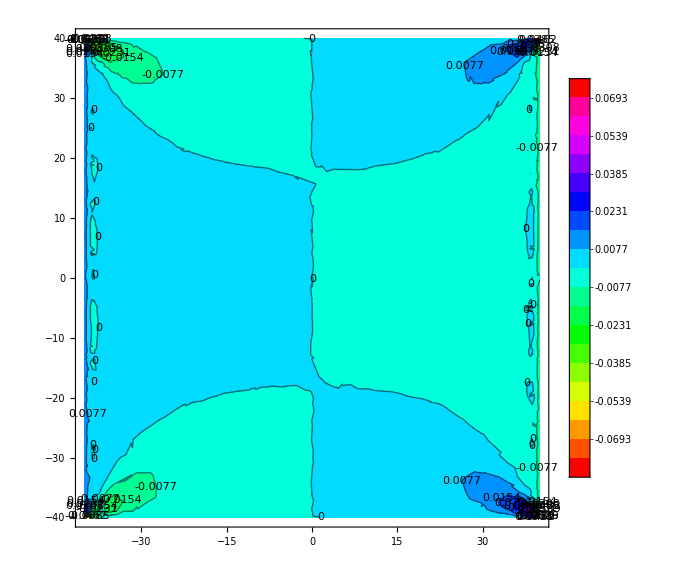

```mathematica
PlotContour[solution20⟦IDsigmayy-2⟧,MeshRegion[mesh],1]
```

#### Velocity field

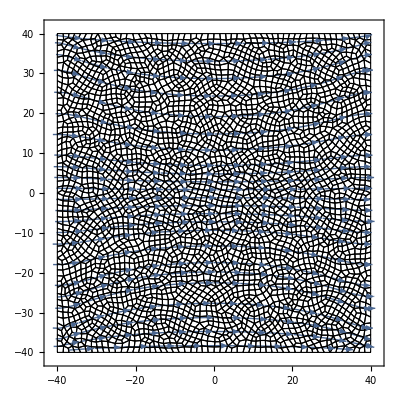

```mathematica
(*in the velocity field we store the velocity vector at the particular point x and y*)
Show[PlotStreamlines[solution20⟦{IDvx-2,IDvy-2}⟧,MeshRegion[mesh],1],MeshPlot]
```

#### Heat flow filed

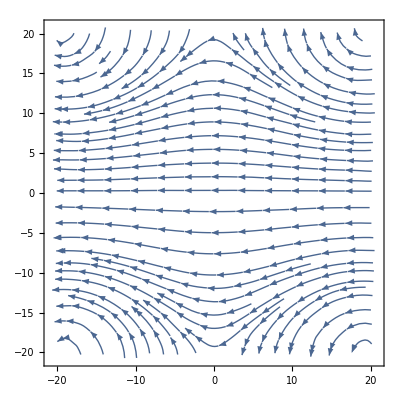

```mathematica
(*in the velocity field we store the velocity vector at the particular point x and y*)
Show[PlotStreamlines[solution20⟦{IDqx-2,IDqy-2}⟧,MeshRegion[mesh],1]]
```